# Lesson 7: Derivatives and Rates of Change

## Exercise 1 - Tangent Line to a Polynomial

```mathematica
f[x_]:=x^4-6 x^2+3x
```

Find the tangent curve to the given function at the point (3,36)

```mathematica
f[3]
```

36

```mathematica
m = f'[3]
```

75

```mathematica
Grid[{{y-f[3]==m(x-3)},
{y = Simplify[m(x-3)+f[3]]}},
Alignment->Right]//TraditionalForm
```

75 x-225==75 (x-3)
75 x-189

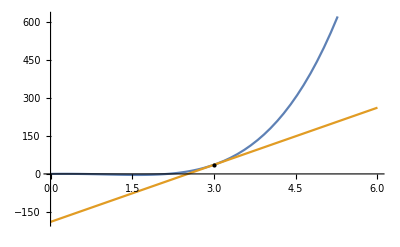

```mathematica
Plot[{f[x],m(x-3)+f[3]},{x,0,6},Epilog->{PointSize[Large], Black, Point[{3,f[3]}]}]
```

## Exercise 2 - Tangent Line to an Algebraic Function

Find the tangent curve to the given function at the point: (2,1/2):

```mathematica
f[x_]:=1/Sqrt[2 x]
```

```mathematica
f'[x]
```

-1/(2 √2 x^(3/2))

```mathematica
f'[2]
```

-1/8

```mathematica
m=f'[2]
```

-1/8

```mathematica
1/8(6-x)==75x-299/2
```

(6-x)/8==-299/2+75 x

```mathematica
Simplify[(2-x)/8+1/2]
```

(6-x)/8

```mathematica
Grid[{{y-f[2]==m(x-2)},
{y==Simplify[m(x-2)+f[2]]}},
Alignment->Right]//TraditionalForm
```

75 x-379/2==(2-x)/8
75 x-189==(6-x)/8

```mathematica
f[x_]:=1/Sqrt[2 x]
```

```mathematica
m = f'[2]
```

-1/8

```mathematica
Grid[{{y - f[2] == m (x - 2)} , { y == Simplify[m (x - 2) + f[2]]}}, 
  Alignment -> Right] // TraditionalForm
```

y-1/2==(2-x)/8
y==(6-x)/8

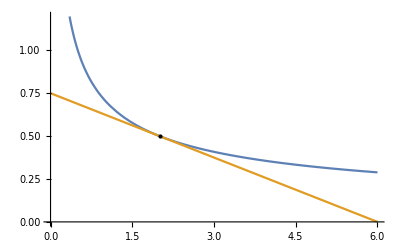

```mathematica
Plot[{f[x],f[2]+m(x-2)},{x,0,6},
Epilog->{PointSize[Large],Black,Point[{2,f[2]}]}]
```

## Exercise 3 - Velocity of a Cannon Ball

```mathematica
h[t_]:=50t -4.9 t^2
```

```mathematica
h'[3]
```

20.6

```mathematica
sol = Solve[{h[t]==0,t>0},t]
```

{{t→10.2041}}

```mathematica
h'[sol[[1,1,2]]]
```

-50.

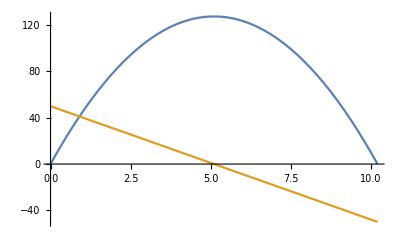

```mathematica
Plot[{h[t],h'[t]},{t,0,sol[[1,1,2]]}]
```

## Exercise 4 - Slope of an Algebraic Function

```mathematica
f[x_]:=2 x^3-9x+Sqrt[x]
```

```mathematica
f'[1]
```

-5/2

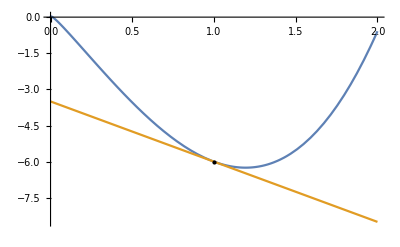

```mathematica
Plot[{f[x],Derivative[1][f][1] (x-1)+f[1]},{x,0,2},Epilog->{Black,PointSize[Large],Point[{1,f[1]}]}]
```

## Exercise 5 - Finding Derivative Using a Table

```mathematica
Grid[{{"t", 0,2,4,6,8,10,12,14},
{"Temperature",62,59,57,59,65,71,75,78}},
Frame->All]
```

t | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14
Temperature | 62 | 59 | 57 | 59 | 65 | 71 | 75 | 78

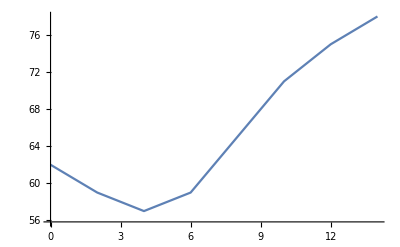

```mathematica
ListLinePlot[
 Transpose[{{0, 2, 4, 6, 8, 10, 12, 14}, {62, 59, 57, 59, 65, 71, 75, 
    78}}]]
```

```mathematica
temperatureData[t_]:=Piecewise[{{62,t==0},{59,t==2},{57,t==4},{59,t==6},{65,t==8},{71,t==10},{75,t==12},{78,t==14}},Undefined];
```

```mathematica
temperatureDerivative[t_]:=
(temperatureData[t]-temperatureData[10])/(t-10)
```

```mathematica
(temperatureDerivative[8]+temperatureDerivative[12]/2)
```

4

```mathematica
temperatureData[t_]:=Piecewise[{{62,t==0},{59,t==2},{57,t==4},{59,t==6},{65,t==8},{71,t==10},{75,t==12},{78,t==14}},Undefined];
```

```mathematica
temperatureDerivative[t_]:=(temperatureData[t]-temperatureData[10])/(t-10)
```

```mathematica
(temperatureDerivative[8] + temperatureDerivative[12])/2
```

5/2